```mathematica
ClearAll["Global`*"]
```

```mathematica
(*定义常微分方程组*)
eqns={
-c U[x]-q U[x]^3+(3/2) q U[x] V[x]-(q/4) U''[x] ,
-c V[x]+(3/4) q V[x]^2-3 q U[x]^2 V[x]+(3 q/4) (U'[x])^2+(3 q/2) U[x] U''[x]-(1/4) q V''[x] 
}/.{U-> Function[x,Subscript[a, 0] +Subscript[a, 1]*P[x]+Subscript[b, 1]*P[x]^(-1)], V-> Function[x,Subscript[c, 0] +Subscript[c, 1]*P[x]+Subscript[c, 2]*P[x]^2+Subscript[d, 1]*P[x]^(-1)+Subscript[d, 2]*P[x]^(-2)]};
```

约束方程：φ'(ξ)=k-(φ(ξ))^2，然后求二次导代入 解的选择来自参考文献
Cakicioglu H, Cinar M, Secer A, et al. On obtaining analytical soliton solutions of Drinfeld-Sokolov-Satsuma-Hirota equation via two efficient methods[J]. Physica Scripta, 2023, 99(1): 015220.

```mathematica
(*使用约束方程进行替换*)
(*转换成关于P的多项式，忽略x*)
SubEqns = eqns/.{P'[x] -> k-P[x]^2}/.{P''[x]->-2*P[x]*(k-P[x]^2)}/.{P[x]->P} ;
(*每一项乘上P四次方，变为正次的多项式*)
expandedEqns=Expand[SubEqns*P^4];
(* P 的各个次幂*)
coeffEqns=Flatten[CoefficientList[expandedEqns,P]];
(*列出方程组*)
eqnList=Thread[coeffEqns==0]
```

{True,-1/2 k^2 q b_1-q b_1^3+3/2 q b_1 d_2==0,-3 q a_0 b_1^2+3/2 q b_1 d_1+3/2 q a_0 d_2==0,-c b_1+1/2 k q b_1-3 q a_0^2 b_1-3 q a_1 b_1^2+3/2 q b_1 c_0+3/2 q a_0 d_1+3/2 q a_1 d_2==0,-c a_0-q a_0^3-6 q a_0 a_1 b_1+3/2 q a_0 c_0+3/2 q b_1 c_1+3/2 q a_1 d_1==0,-c a_1+1/2 k q a_1-3 q a_0^2 a_1-3 q a_1^2 b_1+3/2 q a_1 c_0+3/2 q a_0 c_1+3/2 q b_1 c_2==0,-3 q a_0 a_1^2+3/2 q a_1 c_1+3/2 q a_0 c_2==0,-(q a_1)/2-q a_1^3+3/2 q a_1 c_2==0,15/4 k^2 q b_1^2-3/2 k^2 q d_2-3 q b_1^2 d_2+(3 q d_2^2)/4==0,3 k^2 q a_0 b_1-1/2 k^2 q d_1-3 q b_1^2 d_1-6 q a_0 b_1 d_2+3/2 q d_1 d_2==0,3/2 k^2 q a_1 b_1-9/2 k q b_1^2-3 q b_1^2 c_0-6 q a_0 b_1 d_1+(3 q d_1^2)/4-c d_2+2 k q d_2-3 q a_0^2 d_2-6 q a_1 b_1 d_2+3/2 q c_0 d_2==0,-3 k q a_0 b_1-6 q a_0 b_1 c_0-3 q b_1^2 c_1-c d_1+1/2 k q d_1-3 q a_0^2 d_1-6 q a_1 b_1 d_1+3/2 q c_0 d_1-6 q a_0 a_1 d_2+3/2 q c_1 d_2==0,3/4 k^2 q a_1^2-3 k q a_1 b_1+(3 q b_1^2)/4-c c_0-3 q a_0^2 c_0-6 q a_1 b_1 c_0+(3 q c_0^2)/4-6 q a_0 b_1 c_1-1/2 k^2 q c_2-3 q b_1^2 c_2-6 q a_0 a_1 d_1+3/2 q c_1 d_1-(q d_2)/2-3 q a_1^2 d_2+3/2 q c_2 d_2==0,-3 k q a_0 a_1-6 q a_0 a_1 c_0-c c_1+1/2 k q c_1-3 q a_0^2 c_1-6 q a_1 b_1 c_1+3/2 q c_0 c_1-6 q a_0 b_1 c_2-3 q a_1^2 d_1+3/2 q c_2 d_1==0,-9/2 k q a_1^2+3/2 q a_1 b_1-3 q a_1^2 c_0-6 q a_0 a_1 c_1+(3 q c_1^2)/4-c c_2+2 k q c_2-3 q a_0^2 c_2-6 q a_1 b_1 c_2+3/2 q c_0 c_2==0,3 q a_0 a_1-(q c_1)/2-3 q a_1^2 c_1-6 q a_0 a_1 c_2+3/2 q c_1 c_2==0,(15 q a_1^2)/4-(3 q c_2)/2-3 q a_1^2 c_2+(3 q c_2^2)/4==0}

方程组展示

```mathematica
Exponent[expandedEqns,P]
eqnShow = # ==0&/@coeffEqns /.P->ϕ;
allP=Join[Table[Inactivate[ϕ^n,Power],{n,0,7}],Table[Inactivate[ϕ^n,Power],{n,0,8}]];
Grid[Transpose[{allP,eqnShow }]]
```

{7,8}

ϕ^0 | True
ϕ^1 | -1/2 k^2 q b_1-q b_1^3+3/2 q b_1 d_2==0
ϕ^2 | -3 q a_0 b_1^2+3/2 q b_1 d_1+3/2 q a_0 d_2==0
ϕ^3 | -c b_1+1/2 k q b_1-3 q a_0^2 b_1-3 q a_1 b_1^2+3/2 q b_1 c_0+3/2 q a_0 d_1+3/2 q a_1 d_2==0
ϕ^4 | -c a_0-q a_0^3-6 q a_0 a_1 b_1+3/2 q a_0 c_0+3/2 q b_1 c_1+3/2 q a_1 d_1==0
ϕ^5 | -c a_1+1/2 k q a_1-3 q a_0^2 a_1-3 q a_1^2 b_1+3/2 q a_1 c_0+3/2 q a_0 c_1+3/2 q b_1 c_2==0
ϕ^6 | -3 q a_0 a_1^2+3/2 q a_1 c_1+3/2 q a_0 c_2==0
ϕ^7 | -(q a_1)/2-q a_1^3+3/2 q a_1 c_2==0
ϕ^0 | 15/4 k^2 q b_1^2-3/2 k^2 q d_2-3 q b_1^2 d_2+(3 q d_2^2)/4==0
ϕ^1 | 3 k^2 q a_0 b_1-1/2 k^2 q d_1-3 q b_1^2 d_1-6 q a_0 b_1 d_2+3/2 q d_1 d_2==0
ϕ^2 | 3/2 k^2 q a_1 b_1-9/2 k q b_1^2-3 q b_1^2 c_0-6 q a_0 b_1 d_1+(3 q d_1^2)/4-c d_2+2 k q d_2-3 q a_0^2 d_2-6 q a_1 b_1 d_2+3/2 q c_0 d_2==0
ϕ^3 | -3 k q a_0 b_1-6 q a_0 b_1 c_0-3 q b_1^2 c_1-c d_1+1/2 k q d_1-3 q a_0^2 d_1-6 q a_1 b_1 d_1+3/2 q c_0 d_1-6 q a_0 a_1 d_2+3/2 q c_1 d_2==0
ϕ^4 | 3/4 k^2 q a_1^2-3 k q a_1 b_1+(3 q b_1^2)/4-c c_0-3 q a_0^2 c_0-6 q a_1 b_1 c_0+(3 q c_0^2)/4-6 q a_0 b_1 c_1-1/2 k^2 q c_2-3 q b_1^2 c_2-6 q a_0 a_1 d_1+3/2 q c_1 d_1-(q d_2)/2-3 q a_1^2 d_2+3/2 q c_2 d_2==0
ϕ^5 | -3 k q a_0 a_1-6 q a_0 a_1 c_0-c c_1+1/2 k q c_1-3 q a_0^2 c_1-6 q a_1 b_1 c_1+3/2 q c_0 c_1-6 q a_0 b_1 c_2-3 q a_1^2 d_1+3/2 q c_2 d_1==0
ϕ^6 | -9/2 k q a_1^2+3/2 q a_1 b_1-3 q a_1^2 c_0-6 q a_0 a_1 c_1+(3 q c_1^2)/4-c c_2+2 k q c_2-3 q a_0^2 c_2-6 q a_1 b_1 c_2+3/2 q c_0 c_2==0
ϕ^7 | 3 q a_0 a_1-(q c_1)/2-3 q a_1^2 c_1-6 q a_0 a_1 c_2+3/2 q c_1 c_2==0
ϕ^8 | (15 q a_1^2)/4-(3 q c_2)/2-3 q a_1^2 c_2+(3 q c_2^2)/4==0

```mathematica
(*解代数决定方程组，得到关于 c,a0,a1,b0,b1,b2 的表达式*)
Clear[k,c]
(*添加附加约束条件 AnyTrue[{a1,b1,c1,c2,d1,d2},#!=0&],*)
(*solutions = DeleteCases[solutionsRaw,_?(ContainsAll[#,{a0->0,a1->0,b1->0}]&)] ;*)
addConstraints={q!=0,Not[(Subscript[a, 1]==0&&Subscript[b, 1]==0)||(Subscript[c, 1]==0&&Subscript[c, 2]==0&&Subscript[d, 1]==0&&Subscript[d, 2]==0)]};
solutions=Solve[Join[eqnList,addConstraints],{k,Subscript[a, 0],Subscript[a, 1],Subscript[b, 1],Subscript[c, 0],Subscript[c, 1],Subscript[c, 2],Subscript[d, 1],Subscript[d, 2]}];
solutions//Column
```

{k→-c/q,a_0→0,a_1→-1,b_1→0,c_0→c/q,c_1→0,c_2→1,d_1→0,d_2→0}
{k→-(4 c)/q,a_0→0,a_1→-1/2,b_1→0,c_0→(2 c)/q,c_1→0,c_2→1/2,d_1→0,d_2→0}
{k→-c/q,a_0→-(ⅈ √c)/(2 √q),a_1→-1/2,b_1→0,c_0→c/(2 q),c_1→0,c_2→1/2,d_1→0,d_2→0}
{k→-c/q,a_0→(ⅈ √c)/(2 √q),a_1→-1/2,b_1→0,c_0→c/(2 q),c_1→0,c_2→1/2,d_1→0,d_2→0}
{k→-(4 c)/q,a_0→0,a_1→1/2,b_1→0,c_0→(2 c)/q,c_1→0,c_2→1/2,d_1→0,d_2→0}
{k→-c/q,a_0→-(ⅈ √c)/(2 √q),a_1→1/2,b_1→0,c_0→c/(2 q),c_1→0,c_2→1/2,d_1→0,d_2→0}
{k→-c/q,a_0→(ⅈ √c)/(2 √q),a_1→1/2,b_1→0,c_0→c/(2 q),c_1→0,c_2→1/2,d_1→0,d_2→0}
{k→-c/q,a_0→0,a_1→1,b_1→0,c_0→c/q,c_1→0,c_2→1,d_1→0,d_2→0}
{k→-(4 c)/q,a_0→0,a_1→0,b_1→-(2 c)/q,c_0→(2 c)/q,c_1→0,c_2→0,d_1→0,d_2→(8 c^2)/q^2}
{k→-c/q,a_0→0,a_1→0,b_1→-c/q,c_0→c/q,c_1→0,c_2→0,d_1→0,d_2→c^2/q^2}
{k→-c/q,a_0→-(ⅈ √c)/(2 √q),a_1→0,b_1→-c/(2 q),c_0→c/(2 q),c_1→0,c_2→0,d_1→0,d_2→c^2/(2 q^2)}
{k→-c/q,a_0→(ⅈ √c)/(2 √q),a_1→0,b_1→-c/(2 q),c_0→c/(2 q),c_1→0,c_2→0,d_1→0,d_2→c^2/(2 q^2)}
{k→-c/q,a_0→0,a_1→1/2,b_1→-c/(2 q),c_0→c/q,c_1→0,c_2→1/2,d_1→0,d_2→c^2/(2 q^2)}
{k→-c/(4 q),a_0→0,a_1→1,b_1→-c/(4 q),c_0→c/(2 q),c_1→0,c_2→1,d_1→0,d_2→c^2/(16 q^2)}
{k→-c/(4 q),a_0→-(ⅈ √c)/(2 √q),a_1→1/2,b_1→-c/(8 q),c_0→c/(4 q),c_1→0,c_2→1/2,d_1→0,d_2→c^2/(32 q^2)}
{k→-c/(4 q),a_0→(ⅈ √c)/(2 √q),a_1→1/2,b_1→-c/(8 q),c_0→c/(4 q),c_1→0,c_2→1/2,d_1→0,d_2→c^2/(32 q^2)}
{k→-c/(4 q),a_0→-(ⅈ √c)/(2 √q),a_1→-1/2,b_1→c/(8 q),c_0→c/(4 q),c_1→0,c_2→1/2,d_1→0,d_2→c^2/(32 q^2)}
{k→-c/(4 q),a_0→(ⅈ √c)/(2 √q),a_1→-1/2,b_1→c/(8 q),c_0→c/(4 q),c_1→0,c_2→1/2,d_1→0,d_2→c^2/(32 q^2)}
{k→-c/(4 q),a_0→0,a_1→-1,b_1→c/(4 q),c_0→c/(2 q),c_1→0,c_2→1,d_1→0,d_2→c^2/(16 q^2)}
{k→-c/q,a_0→0,a_1→-1/2,b_1→c/(2 q),c_0→c/q,c_1→0,c_2→1/2,d_1→0,d_2→c^2/(2 q^2)}
{k→-c/q,a_0→-(ⅈ √c)/(2 √q),a_1→0,b_1→c/(2 q),c_0→c/(2 q),c_1→0,c_2→0,d_1→0,d_2→c^2/(2 q^2)}
{k→-c/q,a_0→(ⅈ √c)/(2 √q),a_1→0,b_1→c/(2 q),c_0→c/(2 q),c_1→0,c_2→0,d_1→0,d_2→c^2/(2 q^2)}
{k→-c/q,a_0→0,a_1→0,b_1→c/q,c_0→c/q,c_1→0,c_2→0,d_1→0,d_2→c^2/q^2}
{k→-(4 c)/q,a_0→0,a_1→0,b_1→(2 c)/q,c_0→(2 c)/q,c_1→0,c_2→0,d_1→0,d_2→(8 c^2)/q^2}

挑一些解，最好包含正幂，负幂，正负都有并且简单的

```mathematica
solNice = Flatten[GatherBy[solutions,First[#]&],1];
solNice = solNice[[2;; ;;2]]; (*按偶数选,减少解的数列,从这里面继续选*)

solNice=solNice[[{3,5,7}]];
solNice//Column
```

{k→-c/q,a_0→0,a_1→1,b_1→0,c_0→c/q,c_1→0,c_2→1,d_1→0,d_2→0}
{k→-c/q,a_0→0,a_1→1/2,b_1→-c/(2 q),c_0→c/q,c_1→0,c_2→1/2,d_1→0,d_2→c^2/(2 q^2)}
{k→-c/q,a_0→0,a_1→0,b_1→c/q,c_0→c/q,c_1→0,c_2→0,d_1→0,d_2→c^2/q^2}

c>0, q<0 , k>0

```mathematica
(*(-ρ*√(-k(γ^2-τ^2)-γ √-k Cos[2 √-k(z+Subscript[ξ, 0])]))/(γ*Sin[2 √-k(z+Subscript[ξ, 0])]+τ)*)
(*I*ρ*√-k(1-(2γ)/(γ+Cos[2 √-k(z+Subscript[ξ, 0])]+I*ρ*Sin[2 √-k(z+Subscript[ξ, 0])])) ρ*√k(1-(2γ)/(γ+Cosh[2 √k(z+Subscript[ξ, 0])]+ρ*Sinh[2 √k(z+Subscript[ξ, 0])]));(-ρ √(k(γ^2+τ^2))+γ √k Cosh[2 √k(z+Subscript[ξ, 0])])/(γ*Sinh[2 √k(z+Subscript[ξ, 0])]+τ)*)
(*√k(Tanh[2 √k(z+Subscript[ξ, 0])]-I*ρ*Sech[2 √k(z+Subscript[ξ, 0])])*)
exprPos=√k(Tanh[2 √k(z+Subscript[ξ, 0])]-I*ρ*Sech[2 √k(z+Subscript[ξ, 0])]);
exprNeg=I*ρ*√-k(1-(2γ)/(γ+Cos[2 √-k(z+Subscript[ξ, 0])]+I*ρ*Sin[2 √-k(z+Subscript[ξ, 0])]));
odeolList=Map[
If[
Simplify[k>0/. #,c>0&&q<0],
P[z]->exprPos/. #,P[z]->exprNeg/. #]&,
solNice];
```

```mathematica
vNicer= MapThread[(Subscript[c, 0] +Subscript[c, 1]*P[z]+Subscript[c, 2]*P[z]^2+Subscript[d, 1]*P[z]^(-1)+Subscript[d, 2]*P[z]^(-2)/. #1/. #2/. z->(x-c*t))&,{solNice,odeolList}];
uNicer = MapThread[(Subscript[a, 0] +Subscript[a, 1]*P[z]+Subscript[b, 1]*P[z]^(-1)/. #1/. #2/. z->(x-c*t))&,{solNice ,odeolList}];
Grid[Transpose[{k/.solNice,MapIndexed[Subscript[u, First[#2+8]]->#1&,uNicer],MapIndexed[Subscript[v, First[#2+8]]->#1&//TrigToExp,vNicer]}]]
```

-c/q | u_9→√(-c/q) (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+ξ_0)]+Tanh[2 √(-c/q) (-c t+x+ξ_0)]) | v_9→c/q-(c (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+ξ_0)]+Tanh[2 √(-c/q) (-c t+x+ξ_0)])^2)/q
-c/q | u_10→-c/(2 √(-c/q) q (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+ξ_0)]+Tanh[2 √(-c/q) (-c t+x+ξ_0)]))+1/2 √(-c/q) (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+ξ_0)]+Tanh[2 √(-c/q) (-c t+x+ξ_0)]) | v_10→c/q-c/(2 q (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+ξ_0)]+Tanh[2 √(-c/q) (-c t+x+ξ_0)])^2)-(c (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+ξ_0)]+Tanh[2 √(-c/q) (-c t+x+ξ_0)])^2)/(2 q)
-c/q | u_11→c/(√(-c/q) q (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+ξ_0)]+Tanh[2 √(-c/q) (-c t+x+ξ_0)])) | v_11→c/q-c/(q (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+ξ_0)]+Tanh[2 √(-c/q) (-c t+x+ξ_0)])^2)

ρ 要严格正负1

-Graphics3D-

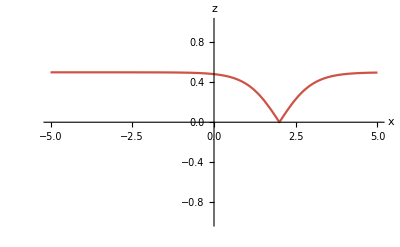

```mathematica
paraC=1;paraQ=-4;
paraX0 =0;paraR =1;
paraT = 5;paraG =4;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap",PlotPoints->70(* 60很顺滑*)
};

f[x_,t_]:=-c/(2 √(-c/q) q (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]))+1/2 √(-c/q) (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
g[x_,t_]:=c/q-c/(2 q (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])^2)-(c (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])^2)/(2 q)/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT};
Plot3D[Abs[f[x,t]],{x,-5,5},{t,0,3},Evaluate[setting1],PlotRange->All,

AxesLabel->{"x","t","u_10"," "}]
Plot[Abs[f[x,2]],{x,-5,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap",PlotRange->{-1,1}]
```

论文图像,参数收集
paraC=1;paraQ=-4;
paraX0 =0;paraR =1;
paraT = 5;paraG =4;

```mathematica
GraphicsRow[
{
Plot3D[Abs[f[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],PlotRange->All,

AxesLabel->{"x","t","|u_10|"," "}],
Plot3D[Abs[g[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],PlotRange->All,
AxesLabel->{"x","t","|v_10|"," "}]
},ImageSize->800]
```

-Graphics-

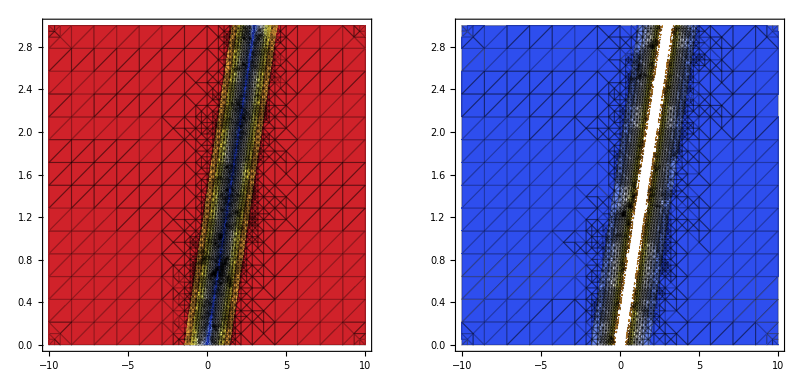

```mathematica
GraphicsRow[
{ContourPlot[Abs[f[x,t]],{x,-10,10},{t,0,3},Mesh->All,PlotRange->All,
ColorFunction->"TemperatureMap"],
ContourPlot[Abs[g[x,t]],{x,-10,10},{t,0,3},Mesh->All,PlotRange->All,
ColorFunction->"TemperatureMap"]},
ImageSize->800]
```

```mathematica
(*原始偏微分方程*)
Peqns={D[u[x,t],t]-3 q u[x,t]^2 D[u[x,t],x]+(3/2) q D[(u[x,t] v[x,t]),x]-(1/4) q D[u[x,t],{x,3}]==0,D[v[x,t],t]+(3/2) q v[x,t] D[v[x,t],x]-3 q D[(u[x,t]^2 v[x,t]),x]+3 q D[u[x,t],x] D[u[x,t],{x,2}]+(3/2) q u[x,t] D[u[x,t],{x,3}]-(1/4) q D[v[x,t],{x,3}]==0};
(*批量验证，虽然笨拙代码，但很快*)
Map[
(Peqns/. 
{u->Function[{x,t},uNicer[[#]]],
v->Function[{x,t},vNicer[[#]]]
}
)&,{Table[i,{i,Length[uNicer]}]}
]
```

{{{0,0,0}==0,{0,0,0}==0}}

```mathematica
Clear[v,u]
```

```mathematica
Peqns/. 
{u->Function[{x,t},-c/(2 √(-c/q) q (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]))+1/2 √(-c/q) (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])],
v->Function[{x,t},c/q-c/(2 q (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])^2)-(c (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])^2)/(2 q)]

}/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->-1,γ->paraG,τ->paraT}//FullSimplify
```

{True,True}